## Definition

```mathematica
δa[r_]=(E^(-r^2/(2 a^2)))/((2π)^(3/2)a^3);α=0.1;u0=10^-20;δstart=10^-10;m=100;αSch=2m;ee={10^-10,10^-5,0.001,0.003,0.007,0.01,0.03,0.07,0.1,0.3,0.7,1};
Vs1[r_,a_,c1_]=- α/r Erf[r/(√2 a)]+c1 a^2 δa[r];
Vs2[r_,a_,{c2_,d1_}]=- 1/# Erf[#/(√2 a)]+c2 a^2 δa[#]+d1 a^4 Laplacian[δa[#],{#,θ,ϕ},"Spherical"]&[r];V[r_]=-α/r;
```

```mathematica
RS[n_,r_]=2/(A^(3/2) n^(3/2)) ⅇ^(-r/(n A)) Hypergeometric1F1[1-n,2,(2 r)/(n A)]/.A->Rationalize@(1/(m α));
```

```mathematica
EigenEnergy[V_,αSch_]:=
Module[{min=1.*10^-19,max=5000,wpc=MachinePrecision,acg=30,sol,ef,evShifted,evnew,steps=∞,stepfraction=10^-2},
PrintTemporary[V];
Module[{shift=10,d=1000,n=20,ev},{ev,ef}=NDEigensystem[{shift f[r]+V f[r]-1/αSch f''[r](*+NeumannValue[0,r==d]*),DirichletCondition[f[r]==0,True]},f[r],{r,0,d},n,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->1}}},"Eigensystem"->{"Arnoldi",MaxIterations->Infinity}}];
evShifted=ev-shift];
Print[evShifted];
sol=ParametricNDSolve[{V u[r]-1/αSch u''[r]==e u[r],u'[max]==-min,u[max]==min},u,{r,min,max},e,MaxSteps->steps,WorkingPrecision->wpc,AccuracyGoal->acg];
evnew=e/.#&/@
Table[
PrintTemporary[n];FindRoot[u[e][min]==0/.sol,{e,0.97 SetPrecision[evShifted[[n]],3],1.03 SetPrecision[evShifted[[n]],3]},WorkingPrecision->wpc,AccuracyGoal->acg,StepMonitor:>PrintTemporary[e]],{n,20}]
]
δ50e[en_,V_]:=Module[{sol,δs,δr,r1=50,r2=u0,β,jder,nder,k},
k=√(2en);
β:=r1 u'[r1]/u[r1]-1;
jder[r_]=D[SphericalBesselJ[0,r],r];
nder[r_]=D[SphericalBesselY[0,r],r];sol=Flatten@NDSolve[{u''[r]+αSch(en-V)u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->15,WorkingPrecision->30, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}(*,SolveDelayed->True*)];
δs=FindRoot[(*u'[r1]/u[r1]==k Cot[k r1+δ]*)Tan[δ]==(k r1 jder[k r1]-β SphericalBesselJ[0,k r1])/(k r1 nder[k r1]-β SphericalBesselY[0,k r1])/.sol,{δ,0},WorkingPrecision->30,AccuracyGoal->20,PrecisionGoal->15];
δr=δ/.δs;
δr=NestWhile[Sign[#](Abs[#]-π)&,δr,Abs[#]>π/2&]
]
δ50[V_]:=Module[{en,len,δen,timestampa,timestampb},
len=Length@ee;
ParallelTable[
timestampa=SessionTime[];
en=ee[[i]];
δen=δ50e[en,V];
timestampb=SessionTime[];
Print[{en,δen},"    ",timestampb-timestampa];
δen,{i,1,len}]
]
Eigenfun[V_,enelist_]:=Module[{},Flatten[With[{r1=2000,r2=1.*10^-50},NDSolve[{V f[r]-1/αSch f''[r]==# f[r],f[r1]==r2,f'[r1]==-r2},f,{r,r1,r2},WorkingPrecision->50,AccuracyGoal->30,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepSize->0.01,Method->{"Shooting","StartingInitialConditions"->{f'[r2]==1,f[r2]==r2}}]]&/@enelist,2]]
```

```mathematica
Eigenfunsin[V_,ene_,rr_]:=
Module[{efunction,amplitude},efunction=Flatten[With[{r1=2000,r2=1.*10^-50},NDSolve[{V f[r]-1/αSch f''[r]==ene f[r],f[r1]==r2,f'[r1]==-r2},f,{r,r1,r2},WorkingPrecision->50,AccuracyGoal->30,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepSize->0.01,Method->{"Shooting","StartingInitialConditions"->{f'[r2]==1,f[r2]==r2}}]],2];
amplitude=NIntegrate[f[r]^2/.#,{r,1.*10^-50,2000}]^-0.5&/@ef;
amplitude f[rr]/.efunction
]
```

```mathematica
δexpminus10=δ50e[10^-10,V[r]]
δexpminus5=δ50e[10^-5,V[r]]
δ50V=δ50[V[r]]
```

NDSolve::precw: 参数函数的精度 ({{200 (1/10000000000+0.1 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) 小于 WorkingPrecision (30.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.000715697934240279725951429919) 小于 WorkingPrecision (30.).

-0.000715697812041209118022926395707

NDSolve::precw: 参数函数的精度 ({{200 (1/100000+0.1 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) 小于 WorkingPrecision (30.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.229818967009051938174672248) 小于 WorkingPrecision (30.).

-0.225896443698594986277156096198

NDSolve::precw: The precision of the differential equation ({{200 (1/10000000000+0.1 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.003+0.1 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.03+0.1 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.3+0.1 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000715697934240279725951429919) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.830064) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.63343) is less than WorkingPrecision (30.).

{1/10000000000,-0.000715697812041209118022926395707}    0.7500071

{0.003,-0.69280548026319619774262958685}    0.9062587

{0.03,0.564638431322361184572763259756}    1.796892

NDSolve::precw: The precision of the differential equation ({{200 (1/100000+0.1 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.007+0.1 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.07+0.1 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.229818967009051938174672248) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.10748) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.384616) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.56081) is less than WorkingPrecision (30.).

{1/100000,-0.225896443698594986277156096198}    0.8125083

{0.007,-0.107069410107916569933917587522}    1.078136

{0.07,0.367174250300206942474944990425}    1.859392

{0.3,-1.00099023947358236030005652197}    3.812538

NDSolve::precw: The precision of the differential equation ({{200 (0.001+0.1 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.01+0.1 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.1+0.1 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.7+0.1 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==3.23272) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.673022) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.0199246) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==0.810945) is less than WorkingPrecision (30.).

{0.001,1.2707953255007696822307575722}    0.8906336

{0.01,-0.592389553473582383272800452013}    0.9687591

{0.1,0.0199219284597025233850215736105}    1.953144

{0.7,0.681379047351237751056181274002}    4.578167

NDSolve::precw: The precision of the differential equation ({{200 (1+0.1 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==10.52984814763170021615515) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{1,1.476112164695455025367665388}    4.453167

{-0.000715697812041209118022926395707,-0.225896443698594986277156096198,1.2707953255007696822307575722,-0.69280548026319619774262958685,-0.107069410107916569933917587522,-0.592389553473582383272800452013,0.564638431322361184572763259756,0.367174250300206942474944990425,0.0199219284597025233850215736105,-1.00099023947358236030005652197,0.681379047351237751056181274002,1.476112164695455025367665388}

## Determine the best 𝒶 value (using V_eff^(a^2))

```mathematica
aa={10,5,1,0.1,0.05,0.01,0.001};
```

```mathematica
hhhc1[en_,a_,c1_?NumberQ]:=δ50e[en,Vs1[r,a,c1]];
evnhhhc1[a_,c1_]:=N[hhhc1[10^-10,a,c1]-δexpminus10,8];
Determinec1[a_]:=Module[{aaa,findroot},aaa=a;
Print[aaa];findroot=FindRoot[hhhc1[10^-10,aaa,c1]==δexpminus10,{c1,-3.,-0.},MaxIterations->200,AccuracyGoal->20,PrecisionGoal->15,WorkingPrecision->30,StepMonitor:>Print[{c1,evnhhhc1[aaa,c1]}]];
Print[c1/.findroot];
c1/.findroot
]
```

```mathematica
Determinec1[0.1]
```

0.1

FindRoot::precw: 参数函数的精度 (hhhc1[1/10000000000,0.1,c1]==-0.000715697812001446475523646599478) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{200 (1/10000000000+1.904809078027228987834754350996781874582110238343 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{200 (1/10000000000+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{200 (1/10000000000+1.90481 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

{-3.,0.000011578083}

{-2.6143608746593890421286921807616401917631235998784,8.2358549×10^-6}

{-1.7543180541551450131982734979317595598724512591489,1.4234245×10^-7}

{-1.7403271018527090611919057878812820022224548235255,-1.0690096×10^-8}

{-1.7413044404652030559814138142184084023077936094704,3.6659709×10^-11}

{-1.7413010992162028879481073168970545866087146367051,1.3024509×10^-14}

{-1.7413010986139397172792032417411113665752198045825,-7.8465581×10^-15}

{-1.7413010992162028879481073168970545866087146367051,1.3024509×10^-14}

{-1.7413010990047106992341901242449057573453621195206,-1.854097×10^-15}

{-1.7413010990047106992341901242449057573453621195206,-1.854097×10^-15}

{-1.7413010988147896990726076050424556999136333844737,-3.6452525×10^-15}

{-1.7413010988147896990726076050424556999136333844737,-3.6452525×10^-15}

{-1.7413010988365177913274115177530489049815458513759,-1.9602678×10^-15}

{-1.7413010988591143504991451118250512502579065889742,-9.7078696×10^-16}

{-1.7413010988365177913274115177530489049815458513759,-1.9602678×10^-15}

{-1.7413010988493447763218808272429348256629720635738,6.1251742×10^-18}

{-1.7413010988467981711925177469953001262921454542309,3.1960098×10^-15}

{-1.7413010988469424676480322653665833078710925714571,-8.2696169×10^-15}

{-1.7413010988493447763218808272429348256629720635738,6.1251742×10^-18}

{-1.7413010988493447763218808272429348256629720635738,6.1251742×10^-18}

{-1.7413010988492127375270228636089478917214539756336,-4.5817424×10^-15}

{-1.7413010988492770834767416542433808117475383262043,9.1286359×10^-16}

{-1.7413010988492770834767416542433808117475383262043,9.1286359×10^-16}

{-1.7413010988492693571850062424825980531890979117393,1.5603132×10^-15}

{-1.7413010988492598844675435978999763906305359395798,-2.7441496×10^-15}

{-1.7413010988492598844675435978999763906305359395798,-2.7441496×10^-15}

{-1.7413010988492601515906144732395936986974364448115,-2.0517774×10^-16}

{-1.7413010988492620111502341696120197749608956355951,-3.1075814×10^-15}

{-1.7413010988492620111502341696120197749608956355951,-3.1075814×10^-15}

{-1.7413010988492620111502341696120197749608956355951,-3.1075814×10^-15}

{-1.7413010988492619771527224087585789317734787958155,-3.6191308×10^-15}

{-1.7413010988492619771527224087585789317734787958155,-3.6191308×10^-15}

{-1.7413010988492619760508356283192290891118139737949,-3.6191308×10^-15}

{-1.7413010988492619762066918449525588612895403050545,-3.6191308×10^-15}

{-1.7413010988492619765937066712505452254818159971129,-3.6191308×10^-15}

{-1.7413010988492619764966352720784732059866077537412,-3.6191308×10^-15}

{-1.7413010988492619763516635585155160336380740293979,-3.6191308×10^-15}

{-1.7413010988492619763025126905322238539434482407955,-3.6191308×10^-15}

{-1.7413010988492619763025126905322238539434482407955,-3.6191308×10^-15}

{-1.7413010988492619763025126905322238539434482407955,-3.6191308×10^-15}

«1 more identical outputs»

{-1.7413010988492619763024923297007399409637045362316,-3.6191308×10^-15}

{-1.7413010988492619763024923297007399409637045362316,-3.6191308×10^-15}

{-1.7413010988492619763024923297007399409637045362316,-3.6191308×10^-15}

{-1.741301098849261976302479085448061485761571319311,-3.6191308×10^-15}

{-1.741301098849261976302469312064353497315881956196,-3.6191308×10^-15}

{-1.7413010988492619763024644253724995030930372746384,-3.6191308×10^-15}

{-1.7413010988492619763024619820265725059816149338597,-3.6191308×10^-15}

{-1.7413010988492619763024619820265725059816149338597,-3.6191308×10^-15}

{-1.7413010988492619763024613839458477121938709409405,-3.6191308×10^-15}

{-1.7413010988492619763024613839458477121938709409405,-3.6191308×10^-15}

{-1.7413010988492619763024612313324215989697697794621,-3.6191308×10^-15}

{-1.7413010988492619763024612313324215989697697794621,-3.6191308×10^-15}

{-1.7413010988492619763024611923770914134380811634611,-3.6191308×10^-15}

{-1.7413010988492619763024611720590831964139548646474,-3.6191308×10^-15}

{-1.7413010988492619763024611720590831964139548646474,-3.6191308×10^-15}

{-1.7413010988492619763024611720590831964139548646474,-3.6191308×10^-15}

«1 more identical outputs»

{-1.741301098849261976302461170868066155432254146884,-3.6191308×10^-15}

{-1.7413010988492619763024611702468334810802925057982,-3.6191308×10^-15}

{-1.7413010988492619763024611699362171439043116852554,-3.6191308×10^-15}

{-1.7413010988492619763024611697809089753163212749839,-3.6191308×10^-15}

{-1.7413010988492619763024611697032548910223260698482,-3.6191308×10^-15}

{-1.7413010988492619763024611697032548910223260698482,-3.6191308×10^-15}

{-1.7413010988492619763024611696842518342546545399795,-3.6191308×10^-15}

{-1.7413010988492619763024611696842518342546545399795,-3.6191308×10^-15}

{-1.7413010988492619763024611696842518342546545399795,-3.6191308×10^-15}

«1 more identical outputs»

{-1.7413010988492619763024611696830897745445952329685,-3.6191308×10^-15}

{-1.7413010988492619763024611696824836443028433688389,-3.6191308×10^-15}

{-1.7413010988492619763024611696821805791819674367741,-3.6191308×10^-15}

{-1.7413010988492619763024611696820290466215294707417,-3.6191308×10^-15}

{-1.7413010988492619763024611696820290466215294707417,-3.6191308×10^-15}

{-1.741301098849261976302461169681991964453021768609,-3.6191308×10^-15}

{-1.7413010988492619763024611696819726223971661281673,-3.6191308×10^-15}

{-1.7413010988492619763024611696819629513692383079464,-3.6191308×10^-15}

{-1.7413010988492619763024611696819581158552743978359,-3.6191308×10^-15}

{-1.7413010988492619763024611696819581158552743978359,-3.6191308×10^-15}

{-1.7413010988492619763024611696819581158552743978359,-3.6191308×10^-15}

{-1.741301098849261976302461169681957536705408021773,-3.6191308×10^-15}

{-1.741301098849261976302461169681957536705408021773,-3.6191308×10^-15}

{-1.7413010988492619763024611696819573888566680243391,-3.6191308×10^-15}

{-1.7413010988492619763024611696819573888566680243391,-3.6191308×10^-15}

{-1.7413010988492619763024611696819573511129833790912,-3.6191308×10^-15}

{-1.7413010988492619763024611696819573314258807622856,-3.6191308×10^-15}

{-1.7413010988492619763024611696819573215823294538829,-3.6191308×10^-15}

{-1.7413010988492619763024611696819573166605537996815,-3.6191308×10^-15}

{-1.7413010988492619763024611696819573141996659725808,-3.6191308×10^-15}

{-1.7413010988492619763024611696819573141996659725808,-3.6191308×10^-15}

{-1.7413010988492619763024611696819573141996659725808,-3.6191308×10^-15}

«2 more identical outputs»

{-1.7413010988492619763024611696819573141290637373054,-3.6191308×10^-15}

{-1.7413010988492619763024611696819573140922376175476,-3.6191308×10^-15}

{-1.7413010988492619763024611696819573140922376175476,-3.6191308×10^-15}

{-1.7413010988492619763024611696819573140832257433053,-3.6191308×10^-15}

{-1.741301098849261976302461169681957314078525150487,-3.6191308×10^-15}

{-1.7413010988492619763024611696819573140761748540779,-3.6191308×10^-15}

{-1.7413010988492619763024611696819573140749997058733,-3.6191308×10^-15}

{-1.7413010988492619763024611696819573140744121317711,-3.6191308×10^-15}

{-1.7413010988492619763024611696819573140744121317711,-3.6191308×10^-15}

{-1.7413010988492619763024611696819573140744121317711,-3.6191308×10^-15}

{-1.7413010988492619763024611696819573140743417579772,-3.6191308×10^-15}

{-1.7413010988492619763024611696819573140743050510125,-3.6191308×10^-15}

{-1.7413010988492619763024611696819573140743050510125,-3.6191308×10^-15}

{-1.7413010988492619763024611696819573140742960682972,-3.6191308×10^-15}

{-1.7413010988492619763024611696819573140742960682972,-3.6191308×10^-15}

{-1.7413010988492619763024611696819573140742960682972,-3.6191308×10^-15}

{-1.7413010988492619763024611696819573140742949459597,-3.6191308×10^-15}

{-1.7413010988492619763024611696819573140742943605486,-3.6191308×10^-15}

{-1.741301098849261976302461169681957314074294067843,-3.6191308×10^-15}

{-1.7413010988492619763024611696819573140742939214902,-3.6191308×10^-15}

{-1.7413010988492619763024611696819573140742938483138,-3.6191308×10^-15}

{-1.7413010988492619763024611696819573140742938117256,-3.6191308×10^-15}

{-1.7413010988492619763024611696819573140742938117256,-3.6191308×10^-15}

{-1.741301098849261976302461169681957314074293802772,-3.6191308×10^-15}

{-1.7413010988492619763024611696819573140742937981018,-3.6191308×10^-15}

{-1.7413010988492619763024611696819573140742937957667,-3.6191308×10^-15}

{-1.7413010988492619763024611696819573140742937957667,-3.6191308×10^-15}

{-1.7413010988492619763024611696819573140742937951952,-3.6191308×10^-15}

{-1.7413010988492619763024611696819573140742937948972,-3.6191308×10^-15}

{-1.7413010988492619763024611696819573140742937947481,-3.6191308×10^-15}

{-1.7413010988492619763024611696819573140742937947481,-3.6191308×10^-15}

{-1.7413010988492619763024611696819573140742937947481,-3.6191308×10^-15}

{-1.7413010988492619763024611696819573140742937947303,-3.6191308×10^-15}

{-1.741301098849261976302461169681957314074293794721,-3.6191308×10^-15}

{-1.741301098849261976302461169681957314074293794721,-3.6191308×10^-15}

{-1.7413010988492619763024611696819573140742937947187,-3.6191308×10^-15}

{-1.7413010988492619763024611696819573140742937947175,-3.6191308×10^-15}

{-1.7413010988492619763024611696819573140742937947169,-3.6191308×10^-15}

{-1.7413010988492619763024611696819573140742937947166,-3.6191308×10^-15}

{-1.7413010988492619763024611696819573140742937947166,-3.6191308×10^-15}

FindRoot::brdig: 根已经被 50. 工作数位紧密包围，但是函数值超过了绝对容差 1.×10^-30.

-1.7413010988492619763024611696819573140742937947165

-1.7413010988492619763024611696819573140742937947165

```mathematica
c1a=Determinec1[#]&/@Drop[aa,-2];
```

10

NDSolve::precw: 参数函数的精度 ({{200 (1/10000000000+0.0190481 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) 小于 WorkingPrecision (30.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.000766857886084515923155506603) 小于 WorkingPrecision (30.).

NDSolve::precw: 参数函数的精度 ({{200 (1.×10^-10+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) 小于 WorkingPrecision (30.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.000736218562981512873463038084) 小于 WorkingPrecision (30.).

NDSolve::precw: 参数函数的精度 ({{200 (1/10000000000+0.0190480907802722909357289914804 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) 小于 WorkingPrecision (30.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.000766857886084516632896281689) 小于 WorkingPrecision (30.).

General::stop: 在本次计算中，FindRoot::precw 的进一步输出将被抑制.

{2.00924440615362507094419939758,3.268082×10^-7}

{1.97774711010285357152189509959,3.9846694×10^-6}

{2.01205850274488364232028449296,-1.1878241×10^-8}

{2.01195980815736121886790702613,4.2484495×10^-11}

{2.01196015989681731658257333256,5.5867635×10^-15}

{2.01196015994307757223538473636,1.0516299×10^-19}

{2.01196015994307844303621182978,2.2084939×10^-20}

{2.01196015994307855847411800243,1.7044887×10^-21}

2.01196015994307855847411800243

5

{-3.,-0.000011738741}

{-3.,-0.000011738741}

{-3.,-0.000011738741}

{-2.985,-0.0000136385}

{-2.83738,-0.000053374378}

{-2.76357,-0.00017147372}

{-2.68977,0.00023103738}

{-2.69379,0.00026216886}

{-2.71023,0.00059593338}

{-2.71845,0.0017128036}

{-2.72667,-0.0018861869}

{-2.72645,-0.0019976171}

{-2.72451,-0.0042555199}

{-2.72353,-0.0097432726}

{-2.72305,-0.0273422}

{-2.72256,0.033966222}

{-2.72259,0.038752377}

{-2.7227,0.089697506}

{-2.72275,0.25858146}

{-2.7228,-0.27397202}

{-2.7228,-0.32392665}

{-2.72279,-0.60910848}

{-2.72278,-0.98667356}

{-2.72277969227762639548018341884,-1.3025524}

{-2.72277684400296049460621361504,1.4599155}

{-2.72277826814029344504319851694,-1.4892127}

{-2.72277791634563378240922652482,-1.5367452}

{-2.72277754899779595619521907055,1.5550522}

{-2.72277773267171486930222279769,-1.5616372}

{-2.72277764064072139135046714409,1.567477}

{-2.7227776867420966955006541778,-1.5678646}

{-2.72277767522538206918868638456,-1.5694262}

{-2.72277767522538206918868638456,-1.5694262}

{-2.72277767234297446708589493405,-1.569817}

{-2.72277767089997257462411712682,-1.5700127}

{-2.72277767089997257462411712682,-1.5700127}

{-2.72277767053939083894692406377,-1.5700616}

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法找到 merit 函数的充足的降低. 您可能需要多于 30. 位工作精度以满足这些容差.

{-2.72277767035893123367007614349,0.00071600299}

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法找到 merit 函数的充足的降低. 您可能需要多于 30. 位工作精度以满足这些容差.

General::stop: 在本次计算中，FindRoot::lstol 的进一步输出将被抑制.

{-2.72277767035901349204713255342,0.00071600299}

{-2.72277767044920216549702830859,0.00071539264}

{-2.72277767044920216549702830859,0.00071539264}

{-2.72277767044922270312327870226,0.00071539264}

{-2.72277767044922270312327870226,0.00071539264}

{-2.72277767044923296723964157574,0.00071539264}

{-2.72277767046049628495613450998,0.00071539264}

{-2.7227776704661279438143809771,0.00071539264}

{-2.7227776704661279438143809771,0.00071539264}

{-2.72277767046612922624428351128,0.00071539264}

{-2.72277767046612922624428351128,0.00071539264}

{-2.722777670466129867167124629,0.00071539264}

{-2.722777670466129867167124629,0.00071539264}

{-2.72277767046613018748257611357,0.00071539264}

{-2.72277767046648168546904267928,0.00071539264}

{-2.72277767046648168546904267928,0.00071539264}

{-2.72277767046648176551143354151,0.00071539264}

{-2.72277767046648176551143354151,0.00071539264}

{-2.72277767046648180551440158892,0.00071539264}

{-2.72277767046652570275062817037,0.00071539264}

{-2.7227776704665476513687414611,0.00071539264}

{-2.72277767046655862567779810646,0.00071539264}

{-2.72277767046656411283232642914,0.00071539264}

{-2.72277767046656685640959059048,0.00071539264}

{-2.72277767046656685640959059048,0.00071539264}

{-2.72277767046656685703435229764,0.00071539264}

{-2.7227776704665675426162874844,0.00071539264}

{-2.72277767046656788540725507777,0.00071539264}

{-2.72277767046656805680273887446,0.00071539264}

{-2.72277767046656805680273887446,0.00071539264}

{-2.72277767046656805684176869748,0.00071539264}

{-2.72277767046656805684176869748,0.00071539264}

{-2.7227776704665680568612747212,0.00071539264}

{-2.72277767046656807826619972817,0.00071539264}

{-2.72277767046656807826619972817,0.00071539264}

{-2.72277767046656807827107401316,0.00071539264}

{-2.72277767046656807827107401316,0.00071539264}

{-2.7227776704665680782735100457,0.00071539264}

{-2.72277767046656808094668908405,0.00071539264}

{-2.72277767046656808094668908405,0.00071539264}

{-2.72277767046656808094729781482,0.00071539264}

{-2.72277767046656808094729781482,0.00071539264}

{-2.72277767046656808094760204159,0.00071539264}

{-2.72277767046656808094760204159,0.00071539264}

{-2.72277767046656808094775408569,0.00071539264}

{-2.72277767046656808094775408569,0.00071539264}

{-2.72277767046656808094783007312,0.00071539264}

{-2.72277767046656808094783007312,0.00071539264}

{-2.72277767046656808094786804954,0.00071539264}

{-2.72277767046656808094786804954,0.00071539264}

{-2.72277767046656808094788702909,0.00071539264}

{-2.72277767046656808096871423676,0.00071539264}

{-2.72277767046656808096871423676,0.00071539264}

{-2.72277767046656808096871897949,0.00071539264}

{-2.72277767046656808097392341004,0.00071539264}

{-2.72277767046656808097652562532,0.00071539264}

{-2.72277767046656808097782673295,0.00071539264}

{-2.72277767046656808097782673295,0.00071539264}

{-2.72277767046656808097782702924,0.00071539264}

{-2.72277767046656808097815215801,0.00071539264}

{-2.72277767046656808097815215801,0.00071539264}

{-2.72277767046656808097815223204,0.00071539264}

{-2.72277767046656808097823347722,0.00071539264}

{-2.72277767046656808097823347722,0.00071539264}

{-2.72277767046656808097823349572,0.00071539264}

{-2.72277767046656808097825379776,0.00071539264}

{-2.72277767046656808097826394878,0.00071539264}

{-2.72277767046656808097826394878,0.00071539264}

{-2.72277767046656808097826395109,0.00071539264}

{-2.72277767046656808097826395109,0.00071539264}

{-2.72277767046656808097826395225,0.00071539264}

{-2.72277767046656808097826521997,0.00071539264}

{-2.72277767046656808097826521997,0.00071539264}

{-2.72277767046656808097826522026,0.00071539264}

{-2.72277767046656808097826522026,0.00071539264}

{-2.7227776704665680809782652204,0.00071539264}

{-2.72277767046656808097826537872,0.00071539264}

{-2.72277767046656808097826545788,0.00071539264}

{-2.72277767046656808097826545788,0.00071539264}

{-2.7227776704665680809782654579,0.00071539264}

{-2.7227776704665680809782654579,0.00071539264}

{-2.72277767046656808097826545791,0.00071539264}

{-2.7227776704665680809782654678,0.00071539264}

{-2.7227776704665680809782654678,0.00071539264}

{-2.72277767046656808097826546781,0.00071539264}

{-2.72277767046656808097826547027,0.00071539264}

{-2.72277767046656808097826547151,0.00071539264}

{-2.72277767046656808097826547151,0.00071539264}

{-2.72277767046656808097826547152,0.00071539264}

{-2.72277767046656808097826547182,0.00071539264}

{-2.72277767046656808097826547182,0.00071539264}

{-2.72277767046656808097826547183,0.00071539264}

{-2.72277767046656808097826547183,0.00071539264}

FindRoot::brdig: 根已经被 30. 工作数位紧密包围，但是函数值超过了绝对容差 1.×10^-20.

-2.72277767046656808097826547183

1

{-3.22029624090066716775872204556,0.000012513862}

{-2.79402176208299192862685395944,-5.5655827×10^-7}

{-2.81138253913198259076299788278,4.9494882×10^-8}

{-2.80996472683321067053723510344,4.6174821×10^-10}

{-2.80995137520266153039436449333,-3.8033418×10^-13}

{-2.80995138619112256125942537532,2.8276894×10^-18}

{-2.80995138619112256118151414274,2.7830862×10^-18}

{-2.80995138619112255632012399625,2.8285807×10^-18}

{-2.8099513861911228585727815441,2.8898062×10^-18}

{-2.80995138619111480569915736342,2.6961633×10^-18}

{-2.80995138619111477633413266748,2.6002311×10^-18}

{-2.80995138619111472658811180805,2.5707389×10^-18}

{-2.80995138619111472605879192889,2.4957693×10^-18}

{-2.80995138619111470843751908262,2.7022495×10^-18}

{-2.80995138619111493905073222991,2.5171722×10^-18}

{-2.80995138619108988939379906747,1.7666248×10^-18}

{-2.8099513861910898747023697361,1.6206334×10^-18}

{-2.80995138619108971161449207813,1.8015335×10^-18}

{-2.80995138619109133576085700975,1.8621056×10^-18}

{-2.8099513861910800688506843508,1.2769956×10^-18}

{-2.80995138619108006884634040962,1.2672802×10^-18}

{-2.80995138619108006827971887392,1.3954758×10^-18}

{-2.80995138619108006884642575771,1.2667612×10^-18}

{-2.80995138619108006905476020666,1.4534382×10^-18}

{-2.80995138619108006743270001629,1.4191007×10^-18}

{-2.8099513861910800806020959629,1.3437633×10^-18}

{-2.80995138619108006884641999449,1.255178×10^-18}

{-2.80995138619108006884579548114,1.2801726×10^-18}

{-2.80995138619108006887778180849,1.2709561×10^-18}

{-2.80995138619108006635152161681,1.3705443×10^-18}

{-2.80995138619108006887291894882,1.2499233×10^-18}

{-2.80995138619108007517615114771,1.346008×10^-18}

{-2.80995138619107998687696180319,1.570493×10^-18}

{-2.80995138619108006887292847681,1.2318617×10^-18}

{-2.80995138619108006887357831776,1.2624722×10^-18}

{-2.80995138619108006884677684089,1.295924×10^-18}

{-2.80995138619108006937580116963,1.4675077×10^-18}

{-2.80995138619108006624411403379,1.4229651×10^-18}

{-2.80995138619108008581839297916,1.2052415×10^-18}

{-2.80995138619108008582424518011,1.2026536×10^-18}

{-2.80995138619108008854388281371,1.3232657×10^-18}

{-2.80995138619108005870605268545,1.3908988×10^-18}

{-2.80995138619108008582688877814,1.1829935×10^-18}

{-2.80995138619108008598596017341,1.323064×10^-18}

{-2.80995138619108008448341896543,1.3180639×10^-18}

{-2.80995138619108009759346579704,1.4816973×10^-18}

{-2.8099513861910800392262513547,1.3949737×10^-18}

{-2.80995138619108034589018264562,1.4385031×10^-18}

{-2.80995138619107888174992000688,1.388755×10^-18}

-2.80995138619108008582688877824

0.1

{-3.,0.000011578083}

{-2.61436,8.235855×10^-6}

{-1.75432,1.423424×10^-7}

{-1.74033,-1.0690086×10^-8}

{-1.7413,3.6668695×10^-11}

{-1.7413,9.4563024×10^-15}

{-1.7413,1.9428961×10^-19}

{-1.74130109905640617640187883808,1.9428961×10^-19}

{-1.74130109905639786389098824757,1.214455×10^-19}

{-1.74130109905639313836223654157,6.8172912×10^-21}

{-1.74130109905639290683282149445,6.8172912×10^-21}

{-1.74130109905639290683282149445,6.8172912×10^-21}

-1.74130109905639290683282149445

0.05

{-3.,0.000015516054}

{-1.53643,4.704632×10^-6}

{-1.04228,-2.6916606×10^-7}

{-1.06902,2.8854822×10^-8}

{-1.06643,1.6621165×10^-10}

{-1.06641,-3.9812309×10^-16}

{-1.06641492374037816226461927727,1.5674926×10^-20}

{-1.066414923740376748506877155,2.1494269×10^-20}

{-1.066414923740376748506877155,2.1494269×10^-20}

{-1.066414923740376748506877155,2.1494269×10^-20}

{-1.06641492374037635161340030418,7.2320762×10^-21}

-1.06641492374037635161340030418

0.01

{0.,-1.2135304×10^-6}

{-0.586489,-1.9207181×10^-7}

{-0.692686,1.2074957×10^-9}

{-0.692023,-8.314678×10^-12}

{-0.692027,-3.5750428×10^-16}

{-0.692027,-6.9471081×10^-20}

{-0.692027,-1.0166992×10^-19}

{-0.692027,-1.0166992×10^-19}

{-0.692027,-1.134223×10^-19}

{-0.692027,-1.134223×10^-19}

{-0.692027473891613786882714975945,-1.134223×10^-19}

{-0.692027473891630216410806308363,8.8293057×10^-20}

{-0.69202747389162302502338257415,-2.1891661×10^-20}

{-0.69202747389162302502338257415,-2.1891661×10^-20}

{-0.69202747389162302502338257415,-2.1891661×10^-20}

«1 more identical outputs»

{-0.692027473891623031025835767129,-2.1891661×10^-20}

{-0.692027473891623045105102349577,-2.1891661×10^-20}

{-0.692027473891623052144735640801,-2.1891661×10^-20}

{-0.692027473891623055664552286413,-2.1891661×10^-20}

{-0.692027473891623055664552286413,-2.1891661×10^-20}

{-0.692027473891623055973787131711,-2.1891661×10^-20}

{-0.692027473891623056699123870465,-2.1891661×10^-20}

{-0.692027473891623057061792239842,-2.1891661×10^-20}

{-0.692027473891623057243126424531,-2.1891661×10^-20}

{-0.692027473891623057243126424531,-2.1891661×10^-20}

{-0.692027473891623057243126424531,-2.1891661×10^-20}

«1 more identical outputs»

{-0.692027473891623057243618288295,-2.1891661×10^-20}

{-0.692027473891623057244771996759,-2.1891661×10^-20}

{-0.692027473891623057244771996759,-2.1891661×10^-20}

{-0.69202747389162305724487335626,-2.1891661×10^-20}

{-0.69202747389162305724487335626,-2.1891661×10^-20}

{-0.692027473891623057244915131032,-2.1891661×10^-20}

{-0.692027473891623057244915131032,-2.1891661×10^-20}

{-0.69202747389162305724493234828,-2.1891661×10^-20}

{-0.69202747389162305724493234828,-2.1891661×10^-20}

{-0.692027473891623057244939444276,-2.1891661×10^-20}

{-0.69202747389162305724495608854,-2.1891661×10^-20}

{-0.692027473891623057244964410672,-2.1891661×10^-20}

{-0.692027473891623057244968571738,-2.1891661×10^-20}

{-0.692027473891623057244968571738,-2.1891661×10^-20}

{-0.69202747389162305724496893731,-2.1891661×10^-20}

{-0.692027473891623057244969794791,-2.1891661×10^-20}

{-0.692027473891623057244970223531,-2.1891661×10^-20}

{-0.692027473891623057244970437901,-2.1891661×10^-20}

{-0.692027473891623057244970545086,-2.1891661×10^-20}

{-0.692027473891623057244970545086,-2.1891661×10^-20}

{-0.692027473891623057244970554503,-2.1891661×10^-20}

{-0.692027473891623057244970576591,-2.1891661×10^-20}

{-0.692027473891623057244970587635,-2.1891661×10^-20}

{-0.692027473891623057244970593157,-2.1891661×10^-20}

{-0.692027473891623057244970595918,-2.1891661×10^-20}

{-0.692027473891623057244970595918,-2.1891661×10^-20}

{-0.692027473891623057244970595918,-2.1891661×10^-20}

{-0.692027473891623057244970595961,-2.1891661×10^-20}

{-0.692027473891623057244970595961,-2.1891661×10^-20}

{-0.692027473891623057244970595978,-2.1891661×10^-20}

{-0.692027473891623057244970595978,-2.1891661×10^-20}

{-0.692027473891623057244970595985,-2.1891661×10^-20}

{-0.692027473891623057244970596002,-2.1891661×10^-20}

{-0.692027473891623057244970596002,-2.1891661×10^-20}

FindRoot::brdig: 根已经被 30. 工作数位紧密包围，但是函数值超过了绝对容差 1.×10^-20.

-0.692027473891623057244970596002

```mathematica
aa={10,5,1,0.1,0.05,0.01,0.001,0.0001}
```

{10,5,1,0.1,0.05,0.01,0.001,0.0001}

```mathematica
Module[{aaa,findroot,Solveδ,hhhc1δ,evnhhhc1δ},aaa=aa[[7]];
Solveδ[en_,V_]:=Module[{sol,δs,δr,r1=50,r2=u0,β,jder,nder,k},
k=√(2en);
β:=r1 u'[r1]/u[r1]-1;
jder[r_]=D[SphericalBesselJ[0,r],r];
nder[r_]=D[SphericalBesselY[0,r],r];sol=Flatten@NDSolve[{u''[r]+αSch(en-V)u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->15,WorkingPrecision->30, MaxSteps->Infinity,InterpolationOrder->All(*,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}*)(*,SolveDelayed->True*)];
δs=FindRoot[(*u'[r1]/u[r1]==k Cot[k r1+δ]*)Tan[δ]==(k r1 jder[k r1]-β SphericalBesselJ[0,k r1])/(k r1 nder[k r1]-β SphericalBesselY[0,k r1])/.sol,{δ,0},WorkingPrecision->30,AccuracyGoal->20,PrecisionGoal->15];
δr=δ/.δs;
δr=NestWhile[Sign[#](Abs[#]-π)&,δr,Abs[#]>π/2&]
];
hhhc1δ[en_,a_,c1_?NumberQ]:=Solveδ[en,Vs1[r,a,c1]];
evnhhhc1δ[a_,c1_]:=N[hhhc1δ[10^-10,a,c1]-δexpminus10,8];
Print[aaa];findroot=FindRoot[hhhc1δ[10^-10,aaa,c1]==δexpminus10,{c1,-1,-0},MaxIterations->200,AccuracyGoal->20,PrecisionGoal->15,WorkingPrecision->30,StepMonitor:>Print[{c1,evnhhhc1δ[aaa,c1]}]];
Print[c1/.findroot];
c1/.findroot
]
```

0.001

NDSolve::precw: 参数函数的精度 ({{200 (1/10000000000+63.4936 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) 小于 WorkingPrecision (30.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.00071568878143788559308416331) 小于 WorkingPrecision (30.).

NDSolve::precw: 参数函数的精度 ({{200 (1.×10^-10+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) 小于 WorkingPrecision (30.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.000715713658381791647522935055) 小于 WorkingPrecision (30.).

NDSolve::precw: 参数函数的精度 ({{200 (1/10000000000+63.4936 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) 小于 WorkingPrecision (30.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.00071568878143788559308416331) 小于 WorkingPrecision (30.).

General::stop: 在本次计算中，FindRoot::precw 的进一步输出将被抑制.

{-1.,9.1527977×10^-9}

{-0.632076897033630290592134591187,-5.4710747×10^-11}

{-0.634263085378850039457655998596,-1.8928276×10^-13}

{-0.634270675035670049876263470855,-3.1970597×10^-19}

{-0.634270675035670049876263470855,-3.1970597×10^-19}

{-0.634270675041507461796356530181,1.26752×10^-19}

{-0.634270675039850186791388646368,-2.5946599×10^-20}

{-0.634270675040131791531049552285,1.5153118×10^-20}

{-0.634270675039850186791388646368,-2.5946599×10^-20}

{-0.634270675039850186791388646368,-2.5946599×10^-20}

{-0.634270675039851563221843243712,-6.2704052×10^-20}

{-0.634270675039851563221843243712,-6.2704052×10^-20}

{-0.634270675039851563221843243712,-6.2704052×10^-20}

«1 more identical outputs»

{-0.634270675039852188818376346838,-4.3748649×10^-20}

{-0.634270675039852188818376346838,-4.3748649×10^-20}

{-0.634270675039852362429215108353,2.661921×10^-20}

{-0.634270675039852296754580383752,2.661921×10^-20}

{-0.634270675039852296754580383752,2.661921×10^-20}

```mathematica
-0.63428104067166306749296825097578751956812491679998888190148967125066184500727`50.
```

```mathematica
AppendTo[c1a,%]
```

```mathematica
c1a[[2]]=%
```

-1.19540780987856421067742549967822951269720541473

```mathematica
c1a
```

{2.01196015994307855847411800243,-2.72277767046656808097826547183,-2.80995138619108008582688877824,-1.74130109905639290683282149445,-1.06641492374037635161340030418,-0.692027473891623057244970596002}

```mathematica
δa=Table[δ50[Vs1[r,aa[[n]],c1a[[n]]]],{n,(Length@aa)-1}];
DumpSave["C:\\Users\\ASUS\\Documents\\TestDump_δa.mx",δa];
```

NDSolve::precw: The precision of the differential equation ({{200 (1/10000000000+0.00051675465390043150185502443396194572033242511159995 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.003+0.00051675465390043150185502443396194572033242511159995 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.03+0.00051675465390043150185502443396194572033242511159995 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.3+0.00051675465390043150185502443396194572033242511159995 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000715697934231356693915641592) is less than WorkingPrecision (30.).

{1/10000000000,-0.000715697812032286090557722723178}    1.765642

NDSolve::precw: The precision of the differential equation ({{200 (1/100000+0.00051675465390043150185502443396194572033242511159995 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.242395) is less than WorkingPrecision (30.).

{0.003,-0.237808025258942968454592217633}    2.375024

NDSolve::precw: The precision of the differential equation ({{200 (0.007+0.00051675465390043150185502443396194572033242511159995 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.229787554680574091352715686) is less than WorkingPrecision (30.).

{1/100000,-0.225866607030782472690896833346}    1.937518

NDSolve::precw: The precision of the differential equation ({{200 (0.001+0.00051675465390043150185502443396194572033242511159995 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==0.279767) is less than WorkingPrecision (30.).

{0.03,0.272792426851204486218475909799}    4.531294

NDSolve::precw: The precision of the differential equation ({{200 (0.07+0.00051675465390043150185502443396194572033242511159995 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.441078) is less than WorkingPrecision (30.).

{0.007,0.415409783809699716181516250067}    2.875026

NDSolve::precw: The precision of the differential equation ({{200 (0.01+0.00051675465390043150185502443396194572033242511159995 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==0.744153) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.001,0.639748753189830391142836075742}    2.57815

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.921205) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.01,-0.74440779155935832037209268735}    3.046904

FindRoot::precw: The precision of the argument function (Tan[δ]==1.88299) is less than WorkingPrecision (30.).

{0.07,1.08260231015661993929353202968}    6.421935

NDSolve::precw: The precision of the differential equation ({{200 (0.1+0.00051675465390043150185502443396194572033242511159995 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.38527) is less than WorkingPrecision (30.).

{0.3,-0.945535217058042382806255556143}    13.953262

NDSolve::precw: The precision of the differential equation ({{200 (0.7+0.00051675465390043150185502443396194572033242511159995 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.473837) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.1,-0.442498874307010800292363004889}    7.5000716

FindRoot::precw: The precision of the argument function (Tan[δ]==0.557637) is less than WorkingPrecision (30.).

{0.7,0.508687312251855852292990713136}    17.422034

NDSolve::precw: The precision of the differential equation ({{200 (1+0.00051675465390043150185502443396194572033242511159995 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==2.9310030062199363746981463) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{1,1.24200035336288086567041188579}    18.843929

NDSolve::precw: The precision of the differential equation ({{200 (1/10000000000+0.015180157654949178764279889312006354702461270106502 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.003+0.015180157654949178764279889312006354702461270106502 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.03+0.015180157654949178764279889312006354702461270106502 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.3+0.015180157654949178764279889312006354702461270106502 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000715697934238223795462452829) is less than WorkingPrecision (30.).

{1/10000000000,-0.000715697812039153188587044745844}    2.203146

NDSolve::precw: The precision of the differential equation ({{200 (1/100000+0.015180157654949178764279889312006354702461270106502 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.827065) is less than WorkingPrecision (30.).

{0.003,-0.69102767073302426911321116977}    2.656276

NDSolve::precw: The precision of the differential equation ({{200 (0.007+0.015180157654949178764279889312006354702461270106502 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.229818877757382274871676839) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.523074) is less than WorkingPrecision (30.).

{1/100000,-0.225896358924420603005870024844}    1.765642

{0.03,-0.481935699918097009650912129687}    4.18754

NDSolve::precw: The precision of the differential equation ({{200 (0.001+0.015180157654949178764279889312006354702461270106502 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.07+0.015180157654949178764279889312006354702461270106502 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==0.0211075) is less than WorkingPrecision (30.).

{0.007,0.0211044055476770780264007939278}    2.937528

NDSolve::precw: The precision of the differential equation ({{200 (0.01+0.015180157654949178764279889312006354702461270106502 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==3.31462) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.001,1.2777864859494378331484289813}    2.984404

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.565047) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.01,-0.514321945216393408233571065699}    3.015654

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0000403752) is less than WorkingPrecision (30.).

{0.07,-0.0000403751748151259667812618241813}    6.781315

NDSolve::precw: The precision of the differential equation ({{200 (0.1+0.015180157654949178764279889312006354702461270106502 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.86345) is less than WorkingPrecision (30.).

{0.3,-1.07826895307875400614548320775}    13.312626

NDSolve::precw: The precision of the differential equation ({{200 (0.7+0.015180157654949178764279889312006354702461270106502 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.449704) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.1,-0.422607814961782133540284740827}    6.703188

FindRoot::precw: The precision of the argument function (Tan[δ]==0.895719) is less than WorkingPrecision (30.).

{0.7,0.730444614212567124981860002958}    14.781388

NDSolve::precw: The precision of the differential equation ({{200 (1+0.015180157654949178764279889312006354702461270106502 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==24.756260463371931245304869) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{1,1.530424452119108186113099025}    17.078286

NDSolve::precw: The precision of the differential equation ({{200 (1/10000000000+0.17841403031981232651128502722977359153837918872548 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.003+0.17841403031981232651128502722977359153837918872548 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.03+0.17841403031981232651128502722977359153837918872548 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.3+0.17841403031981232651128502722977359153837918872548 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000715697934233693006605399361) is less than WorkingPrecision (30.).

{1/10000000000,-0.000715697812034622402050766765247}    1.859393

NDSolve::precw: The precision of the differential equation ({{200 (1/100000+0.17841403031981232651128502722977359153837918872548 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.834591) is less than WorkingPrecision (30.).

{0.003,-0.695479858228020837210083133775}    2.515649

NDSolve::precw: The precision of the differential equation ({{200 (0.007+0.17841403031981232651128502722977359153837918872548 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.499917) is less than WorkingPrecision (30.).

{0.03,0.463581427398819014741802566224}    3.515658

NDSolve::precw: The precision of the differential equation ({{200 (0.07+0.17841403031981232651128502722977359153837918872548 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.229819766538541587988687511) is less than WorkingPrecision (30.).

{1/100000,-0.225897203117880763429980926264}    2.390647

NDSolve::precw: The precision of the differential equation ({{200 (0.001+0.17841403031981232651128502722977359153837918872548 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.330196) is less than WorkingPrecision (30.).

{0.007,-0.31892468112908755742878559028}    2.750027

NDSolve::precw: The precision of the differential equation ({{200 (0.01+0.17841403031981232651128502722977359153837918872548 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==3.0125) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.001,1.25029131841785561078183033398}    2.343774

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.728215) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.01,-0.629412088205582776930685829415}    2.328146

FindRoot::precw: The precision of the argument function (Tan[δ]==0.243098) is less than WorkingPrecision (30.).

{0.07,0.238471903623707057255361210291}    4.796922

NDSolve::precw: The precision of the differential equation ({{200 (0.1+0.17841403031981232651128502722977359153837918872548 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.83666) is less than WorkingPrecision (30.).

{0.3,-1.07221029559694897015093431854}    9.2813369

NDSolve::precw: The precision of the differential equation ({{200 (0.7+0.17841403031981232651128502722977359153837918872548 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.258935) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.1,-0.25336997725452626418404309318}    5.015671

FindRoot::precw: The precision of the argument function (Tan[δ]==0.618861) is less than WorkingPrecision (30.).

{0.7,0.554172599021471615319733896599}    11.171981

NDSolve::precw: The precision of the differential equation ({{200 (1+0.17841403031981232651128502722977359153837918872548 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==2.0391428253479597867256451) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{1,1.11485644691582756236947221062}    12.125413

NDSolve::precw: The precision of the differential equation ({{200 (1/10000000000+1.10562 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.003+1.10562 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.03+1.10562 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.3+1.10562 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000715697934242552718146125003) is less than WorkingPrecision (30.).

{1/10000000000,-0.000715697812043482109053341983458}    1.546892

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.830166) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (1/100000+1.10562 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

{0.003,-0.692865881884370312661629617256}    1.843769

NDSolve::precw: The precision of the differential equation ({{200 (0.007+1.10562 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.627543) is less than WorkingPrecision (30.).

{0.03,0.560425573584078565224030060109}    3.046904

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.22981898429502719956866788) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.07+1.10562 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

{1/100000,-0.22589646011738303408573915309}    1.70314

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.111092) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.001+1.10562 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

{0.007,-0.110637910941697089397433969284}    2.109398

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{200 (0.01+1.10562 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==3.22732) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.001,1.270323264131670030314886308}    1.484397

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.674526) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.01,-0.593423821983585025630975218944}    2.156267

FindRoot::precw: The precision of the argument function (Tan[δ]==0.375494) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.57831) is less than WorkingPrecision (30.).

{0.07,0.359203790326174611559552161403}    4.406291

{0.3,-1.00604418731991915633058614026}    7.6094479

NDSolve::precw: The precision of the differential equation ({{200 (0.1+1.10562 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.7+1.10562 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00735536) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.1,-0.00735522447508504384482548069207}    3.718787

FindRoot::precw: The precision of the argument function (Tan[δ]==0.771392) is less than WorkingPrecision (30.).

{0.7,0.657052002652187785316148879143}    8.6094548

NDSolve::precw: The precision of the differential equation ({{200 (1+1.10562 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==8.9739925112056042266151271) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{1,1.4598210332026957296868186807}    9.8282187

NDSolve::precw: The precision of the differential equation ({{200 (1/10000000000+1.35421 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.003+1.35421 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.03+1.35421 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.3+1.35421 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000715697934240801436116502156) is less than WorkingPrecision (30.).

{1/10000000000,-0.000715697812041730827920766545964}    1.281263

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.830112) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (1/100000+1.35421 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

{0.003,-0.692834052948703514776054183474}    1.562516

NDSolve::precw: The precision of the differential equation ({{200 (0.007+1.35421 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.229818975167903481596511727) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.630569) is less than WorkingPrecision (30.).

{1/100000,-0.22589645144814064084320692228}    1.343765

{0.03,0.56259416647846395468027127453}    2.640651

NDSolve::precw: The precision of the differential equation ({{200 (0.001+1.35421 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.109187) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.07+1.35421 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

{0.007,-0.108755859592028377256221377867}    1.984393

FindRoot::precw: The precision of the argument function (Tan[δ]==3.23016) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.01+1.35421 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

{0.001,1.2705722185316596364276721826}    1.484388

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.673738) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.01,-0.592882163637203534945893842968}    2.078145

FindRoot::precw: The precision of the argument function (Tan[δ]==0.380035) is less than WorkingPrecision (30.).

{0.07,0.363177414002682750529784805347}    4.015663

NDSolve::precw: The precision of the differential equation ({{200 (0.1+1.35421 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.5706) is less than WorkingPrecision (30.).

{0.3,-1.00382856917583202052355973876}    7.9063255

NDSolve::precw: The precision of the differential equation ({{200 (0.7+1.35421 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.00575547) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.1,0.00575541112518823715407133479177}    3.921914

FindRoot::precw: The precision of the argument function (Tan[δ]==0.784482) is less than WorkingPrecision (30.).

{0.7,0.665206844024445528608611520251}    9.031335

NDSolve::precw: The precision of the differential equation ({{200 (1+1.35421 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==9.4466664154945836317915032) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{1,1.46533164703942667611019442}    10.093845

NDSolve::precw: The precision of the differential equation ({{200 (1/10000000000+4.39393 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.003+4.39393 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.03+4.39393 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.3+4.39393 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000715697934258736150809178982) is less than WorkingPrecision (30.).

{1/10000000000,-0.000715697812059665533426865153223}    3.343781

NDSolve::precw: The precision of the differential equation ({{200 (1/100000+4.39393 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.830064) is less than WorkingPrecision (30.).

{0.003,-0.692805621981951147871308501055}    3.812535

NDSolve::precw: The precision of the differential equation ({{200 (0.007+4.39393 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.229818967055345676221037713) is less than WorkingPrecision (30.).

{1/100000,-0.22589644374256630199932980302}    3.906294

NDSolve::precw: The precision of the differential equation ({{200 (0.001+4.39393 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.107489) is less than WorkingPrecision (30.).

{0.007,-0.107077757952858492071076420031}    5.234425

FindRoot::precw: The precision of the argument function (Tan[δ]==0.633416) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.01+4.39393 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

{0.03,0.564628119190840330295936738451}    9.843842

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{200 (0.07+4.39393 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==3.2327) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.001,1.2707942182214262994995456396}    3.671902

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.673026) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.01,-0.592392007214012146038788272337}    5.812554

FindRoot::precw: The precision of the argument function (Tan[δ]==0.384592) is less than WorkingPrecision (30.).

{0.07,0.367153621404912310015559094039}    10.578225

NDSolve::precw: The precision of the differential equation ({{200 (0.1+4.39393 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.56086) is less than WorkingPrecision (30.).

{0.3,-1.00100609165858388936121612581}    24.031475

NDSolve::precw: The precision of the differential equation ({{200 (0.7+4.39393 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.0198492) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.1,0.0198466155605113736558123963219}    11.265732

FindRoot::precw: The precision of the argument function (Tan[δ]==0.810761) is less than WorkingPrecision (30.).

{0.7,0.681267892268641766355873337802}    24.953361

NDSolve::precw: The precision of the differential equation ({{200 (1+4.39393 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==10.521784614051349852524869) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{1,1.476040035417158988378899125}    28.390895

NDSolve::precw: The precision of the differential equation ({{200 (1/10000000000+40.2721 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.003+40.2721 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.03+40.2721 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.3+40.2721 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000715697934243931559472633214) is less than WorkingPrecision (30.).

{1/10000000000,-0.00071569781204486094967357558055}    391.6287

NDSolve::precw: The precision of the differential equation ({{200 (1/100000+40.2721 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.830064) is less than WorkingPrecision (30.).

{0.003,-0.692805480294573797565498223617}    464.535639

NDSolve::precw: The precision of the differential equation ({{200 (0.007+40.2721 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.22981896701022439428710404) is less than WorkingPrecision (30.).

{1/100000,-0.225896443699708623673190181564}    430.269692

NDSolve::precw: The precision of the differential equation ({{200 (0.001+40.2721 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.10748) is less than WorkingPrecision (30.).

{0.007,-0.107069411497371239338074786125}    705.694167

NDSolve::precw: The precision of the differential equation ({{200 (0.01+40.2721 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==0.63343) is less than WorkingPrecision (30.).

{0.03,0.564638429931464124827139146512}    1179.464263

NDSolve::precw: The precision of the differential equation ({{200 (0.07+40.2721 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==3.23272) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.001,1.270795325042822266021876944}    492.879653

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.673022) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.01,-0.592389553851644493092361333422}    607.721373

$Aborted

```mathematica
δa=δa~Join~Evaluate[δ50[Vs1[r,aa[[8]],c1a[[8]]]]]
```

```mathematica
DumpSave["C:\\Users\\ASUS\\Documents\\TestDump_δa.mx",δa];
```

```mathematica
Δa=Abs[δa[[#]]-δ50V]&/@Range@Length[aa];
La=Transpose@({ee}~Join~{Δa[[#]]})&/@Range@Length[aa];
```

NDSolve::precw: The precision of the differential equation ({{200 (1/10000000000+0.00051675465390043150185502443396194572033242511159995 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (0.003+0.00051675465390043150185502443396194572033242511159995 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (0.03+0.00051675465390043150185502443396194572033242511159995 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (0.3+0.00051675465390043150185502443396194572033242511159995 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

{1/10000000000,-0.000715697811998678854018869984054}    1.782259

NDSolve::precw: The precision of the differential equation ({{200 (1/100000+0.00051675465390043150185502443396194572033242511159995 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.242395) is less than WorkingPrecision (30.).

{0.003,-0.237808026850563003993411992345}    2.001414

NDSolve::precw: The precision of the differential equation ({{200 (0.007+0.00051675465390043150185502443396194572033242511159995 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

{1/100000,-0.225866607022358812596115847932}    1.615141

NDSolve::precw: The precision of the differential equation ({{200 (0.001+0.00051675465390043150185502443396194572033242511159995 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==0.441078) is less than WorkingPrecision (30.).

{0.007,0.415409783777630157008050633064}    3.224278

NDSolve::precw: The precision of the differential equation ({{200 (0.01+0.00051675465390043150185502443396194572033242511159995 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==0.744153) is less than WorkingPrecision (30.).

{0.001,0.639748754857640613750775268291}    2.49176

FindRoot::precw: The precision of the argument function (Tan[δ]==0.279767) is less than WorkingPrecision (30.).

{0.03,0.272792426713670696028334852346}    7.047979

NDSolve::precw: The precision of the differential equation ({{200 (0.07+0.00051675465390043150185502443396194572033242511159995 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.921205) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.01,-0.74440779159435215522605320268}    3.682602

FindRoot::precw: The precision of the argument function (Tan[δ]==1.88299) is less than WorkingPrecision (30.).

{0.07,1.08260229592595935246382220599}    6.999945

NDSolve::precw: The precision of the differential equation ({{200 (0.1+0.00051675465390043150185502443396194572033242511159995 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.38527) is less than WorkingPrecision (30.).

{0.3,-0.94553521739791815117849618331}    17.889638

NDSolve::precw: The precision of the differential equation ({{200 (0.7+0.00051675465390043150185502443396194572033242511159995 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.473837) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.1,-0.442498874512436467640554912432}    8.2188057

FindRoot::precw: The precision of the argument function (Tan[δ]==0.557637) is less than WorkingPrecision (30.).

{0.7,0.508687311948679756988726277285}    20.869744

NDSolve::precw: The precision of the differential equation ({{200 (1+0.00051675465390043150185502443396194572033242511159995 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

{1,1.24200034649273906785358054367}    22.593963

NDSolve::precw: The precision of the differential equation ({{200 (1/10000000000+0.015180157654949178764279889312006354702461270106502 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (0.003+0.015180157654949178764279889312006354702461270106502 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (0.03+0.015180157654949178764279889312006354702461270106502 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (0.3+0.015180157654949178764279889312006354702461270106502 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

{1/10000000000,-0.000715697812001514521940158441225}    2.008419

NDSolve::precw: The precision of the differential equation ({{200 (1/100000+0.015180157654949178764279889312006354702461270106502 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.827065) is less than WorkingPrecision (30.).

{0.003,-0.691027670535915881471420656992}    2.707911

NDSolve::precw: The precision of the differential equation ({{200 (0.007+0.015180157654949178764279889312006354702461270106502 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

{1/100000,-0.225896358912831818772308115102}    2.384685

NDSolve::precw: The precision of the differential equation ({{200 (0.001+0.015180157654949178764279889312006354702461270106502 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==3.31462) is less than WorkingPrecision (30.).

{0.001,1.2777864897934551124360377388}    2.470745

FindRoot::precw: The precision of the argument function (Tan[δ]==0.0211075) is less than WorkingPrecision (30.).

{0.007,0.0211044050184646461250786876983}    4.426126

NDSolve::precw: The precision of the differential equation ({{200 (0.01+0.015180157654949178764279889312006354702461270106502 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.523074) is less than WorkingPrecision (30.).

{0.03,-0.481935708392256448496516679974}    8.29686

NDSolve::precw: The precision of the differential equation ({{200 (0.07+0.015180157654949178764279889312006354702461270106502 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.565047) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.01,-0.514321945093670420374074778028}    4.105901

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0000403757) is less than WorkingPrecision (30.).

{0.07,-0.0000403756590868346077109211800259}    10.694556

NDSolve::precw: The precision of the differential equation ({{200 (0.1+0.015180157654949178764279889312006354702461270106502 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.86345) is less than WorkingPrecision (30.).

{0.3,-1.07826895337210723360680326113}    21.182965

NDSolve::precw: The precision of the differential equation ({{200 (0.7+0.015180157654949178764279889312006354702461270106502 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.449704) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.1,-0.422607815199489195480066350122}    10.350312

FindRoot::precw: The precision of the argument function (Tan[δ]==0.895719) is less than WorkingPrecision (30.).

{0.7,0.730444612823955164347172917594}    23.619686

NDSolve::precw: The precision of the differential equation ({{200 (1+0.015180157654949178764279889312006354702461270106502 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

{1,1.530424451628602567294917941}    28.421078

NDSolve::precw: The precision of the differential equation ({{200 (1/10000000000+0.17841403031981232651128502722977359153837918872548 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (0.003+0.17841403031981232651128502722977359153837918872548 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (0.03+0.17841403031981232651128502722977359153837918872548 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (0.3+0.17841403031981232651128502722977359153837918872548 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.834591) is less than WorkingPrecision (30.).

{1/10000000000,-0.000715697812000040837846425793019}    1.917354

{0.003,-0.695479858175272957868737052355}    1.82529

NDSolve::precw: The precision of the differential equation ({{200 (1/100000+0.17841403031981232651128502722977359153837918872548 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (0.007+0.17841403031981232651128502722977359153837918872548 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.330196) is less than WorkingPrecision (30.).

{1/100000,-0.225897203103518747461068620951}    1.814282

{0.007,-0.318924679965289021703510936678}    1.88233

NDSolve::precw: The precision of the differential equation ({{200 (0.001+0.17841403031981232651128502722977359153837918872548 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (0.01+0.17841403031981232651128502722977359153837918872548 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==0.499917) is less than WorkingPrecision (30.).

{0.03,0.463581427482878985195900124615}    5.121618

NDSolve::precw: The precision of the differential equation ({{200 (0.07+0.17841403031981232651128502722977359153837918872548 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==3.0125) is less than WorkingPrecision (30.).

{0.001,1.25029132100696331624013063898}    1.946375

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.728215) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.01,-0.629412087965808168641044669618}    3.674596

FindRoot::precw: The precision of the argument function (Tan[δ]==0.243098) is less than WorkingPrecision (30.).

{0.07,0.238471903327749010710863916224}    5.53391

NDSolve::precw: The precision of the differential equation ({{200 (0.1+0.17841403031981232651128502722977359153837918872548 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.83666) is less than WorkingPrecision (30.).

{0.3,-1.07221029582393101414427501005}    13.472518

NDSolve::precw: The precision of the differential equation ({{200 (0.7+0.17841403031981232651128502722977359153837918872548 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.258935) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.1,-0.253369977040476876212893376851}    5.63298

FindRoot::precw: The precision of the argument function (Tan[δ]==0.618861) is less than WorkingPrecision (30.).

{0.7,0.554172598755459017171464082342}    13.098254

NDSolve::precw: The precision of the differential equation ({{200 (1+0.17841403031981232651128502722977359153837918872548 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

{1,1.11485643633011608121466748479}    16.001304

NDSolve::precw: The precision of the differential equation ({{200 (1/10000000000+1.10562 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (0.003+1.10562 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (0.03+1.10562 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (0.3+1.10562 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

{1/10000000000,-0.000715697812005065606334072283491}    1.482047

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.830166) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (1/100000+1.10562 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

{0.003,-0.69286588179335236300533103546}    1.633153

NDSolve::precw: The precision of the differential equation ({{200 (0.007+1.10562 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

{1/100000,-0.225896460110085142536730361938}    1.321935

NDSolve::precw: The precision of the differential equation ({{200 (0.001+1.10562 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.111092) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.627543) is less than WorkingPrecision (30.).

{0.007,-0.110637907166469725660582896824}    2.130506

{0.03,0.560425573038148451607515340338}    3.781671

FindRoot::precw: The precision of the argument function (Tan[δ]==3.22732) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.01+1.10562 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (0.07+1.10562 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

{0.001,1.2703232685336893044993712311}    1.378973

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.674526) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.01,-0.593423821384849102142051909774}    2.233577

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.57831) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.375494) is less than WorkingPrecision (30.).

{0.3,-1.00604418778424544021079791274}    8.5530422

{0.07,0.359203789416393283932326452703}    4.863436

NDSolve::precw: The precision of the differential equation ({{200 (0.7+1.10562 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (0.1+1.10562 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00735536) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.1,-0.00735522828503535744004291397635}    4.536205

FindRoot::precw: The precision of the argument function (Tan[δ]==0.771392) is less than WorkingPrecision (30.).

{0.7,0.6570520021511948627772757773}    10.179191

NDSolve::precw: The precision of the differential equation ({{200 (1+1.10562 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

{1,1.4598210328192431073069818841}    11.06982

NDSolve::precw: The precision of the differential equation ({{200 (1/10000000000+1.35421 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (0.003+1.35421 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (0.03+1.35421 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (0.3+1.35421 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

{1/10000000000,-0.000715697812003217687558648574562}    1.185837

NDSolve::precw: The precision of the differential equation ({{200 (1/100000+1.35421 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.830112) is less than WorkingPrecision (30.).

{0.003,-0.69283405280284653837781299716}    1.539087

NDSolve::precw: The precision of the differential equation ({{200 (0.007+1.35421 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

{1/100000,-0.225896451435860605770833207111}    1.382977

NDSolve::precw: The precision of the differential equation ({{200 (0.001+1.35421 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.109187) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.630569) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==3.23016) is less than WorkingPrecision (30.).

{0.007,-0.108755859553676160303310769727}    2.183543

{0.03,0.562594166191040161195756335081}    3.769663

{0.001,1.2705722213243362129061791596}    1.326938

NDSolve::precw: The precision of the differential equation ({{200 (0.01+1.35421 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (0.07+1.35421 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.673738) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.01,-0.592882163547808277036623470339}    2.313634

FindRoot::precw: The precision of the argument function (Tan[δ]==0.380035) is less than WorkingPrecision (30.).

{0.07,0.363177413555492795539909471613}    4.004829

NDSolve::precw: The precision of the differential equation ({{200 (0.1+1.35421 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.5706) is less than WorkingPrecision (30.).

{0.3,-1.0038285695840497848073499679}    9.2755526

NDSolve::precw: The precision of the differential equation ({{200 (0.7+1.35421 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.00575547) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.1,0.00575540958758625103537028075369}    4.335063

FindRoot::precw: The precision of the argument function (Tan[δ]==0.784482) is less than WorkingPrecision (30.).

{0.7,0.665206842472142554095683916273}    9.8219386

NDSolve::precw: The precision of the differential equation ({{200 (1+1.35421 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

{1,1.465331646074083703290557031}    10.813639

NDSolve::precw: The precision of the differential equation ({{200 (1/10000000000+4.39393 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (0.003+4.39393 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (0.03+4.39393 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (0.3+4.39393 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

{1/10000000000,-0.000715697812002797726273996909095}    1.876326

NDSolve::precw: The precision of the differential equation ({{200 (1/100000+4.39393 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.830064) is less than WorkingPrecision (30.).

{1/100000,-0.22589644372574441541391266753}    3.243291

{0.003,-0.692805621878037004883095512323}    4.89746

NDSolve::precw: The precision of the differential equation ({{200 (0.001+4.39393 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (0.007+4.39393 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==3.2327) is less than WorkingPrecision (30.).

{0.001,1.2707942222934784450063958349}    2.323641

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.107489) is less than WorkingPrecision (30.).

{0.007,-0.107077755507137829923138188495}    4.944493

NDSolve::precw: The precision of the differential equation ({{200 (0.01+4.39393 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==0.633416) is less than WorkingPrecision (30.).

{0.03,0.56462811888382994456753762307}    10.971751

NDSolve::precw: The precision of the differential equation ({{200 (0.07+4.39393 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.673026) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.01,-0.592392006956687373166672886162}    5.240703

FindRoot::precw: The precision of the argument function (Tan[δ]==0.384592) is less than WorkingPrecision (30.).

{0.07,0.367153621965816749557552426575}    11.450089

NDSolve::precw: The precision of the differential equation ({{200 (0.1+4.39393 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.56086) is less than WorkingPrecision (30.).

{0.3,-1.0010060918121721706417220725}    25.959338

NDSolve::precw: The precision of the differential equation ({{200 (0.7+4.39393 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.0198492) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.1,0.0198466163011785906925194248873}    11.02418

FindRoot::precw: The precision of the argument function (Tan[δ]==0.810761) is less than WorkingPrecision (30.).

{0.7,0.681267890839556515323077870971}    20.990567

NDSolve::precw: The precision of the differential equation ({{200 (1+4.39393 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

{1,1.476040035037147958767926004}    22.047088

NDSolve::precw: The precision of the differential equation ({{200 (1/10000000000+40.2721 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (0.003+40.2721 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (0.03+40.2721 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (0.3+40.2721 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

{1/10000000000,-0.000715697812003986423720055446855}    162.407722

NDSolve::precw: The precision of the differential equation ({{200 (1/100000+40.2721 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.830064) is less than WorkingPrecision (30.).

{0.003,-0.692805480210429751610895900212}    287.611973

NDSolve::precw: The precision of the differential equation ({{200 (0.007+40.2721 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

{1/100000,-0.225896443685870778133180860365}    168.204643

NDSolve::precw: The precision of the differential equation ({{200 (0.001+40.2721 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==3.23272) is less than WorkingPrecision (30.).

{0.001,1.27079532850045369727040167}    218.564472

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.10748) is less than WorkingPrecision (30.).

{0.007,-0.107069406084231171639242135909}    368.737706

NDSolve::precw: The precision of the differential equation ({{200 (0.01+40.2721 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==0.63343) is less than WorkingPrecision (30.).

{0.03,0.564638428820594922108684858691}    859.6171465

NDSolve::precw: The precision of the differential equation ({{200 (0.07+40.2721 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.673022) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.01,-0.592389554114643799626339969445}    435.019554

FindRoot::precw: The precision of the argument function (Tan[δ]==0.384616) is less than WorkingPrecision (30.).

{0.07,0.367174246636222682226765760859}    773.1944771

NDSolve::precw: The precision of the differential equation ({{200 (0.1+40.2721 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.56081) is less than WorkingPrecision (30.).

{0.3,-1.00099024149958172075027392642}    2153.706384

NDSolve::precw: The precision of the differential equation ({{200 (0.7+40.2721 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.0199246) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.1,0.0199219173992156022959931407773}    1070.379549

FindRoot::precw: The precision of the argument function (Tan[δ]==0.810945) is less than WorkingPrecision (30.).

{0.7,0.681379032649136291884086490325}    1961.514249

NDSolve::precw: The precision of the differential equation ({{200 (1+40.2721 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

{1,1.476112155415772754358866265}    1960.988771

NDSolve::precw: The precision of the differential equation ({{200 (1/10000000000+399.375 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (0.003+399.375 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (0.03+399.375 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (0.3+399.375 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

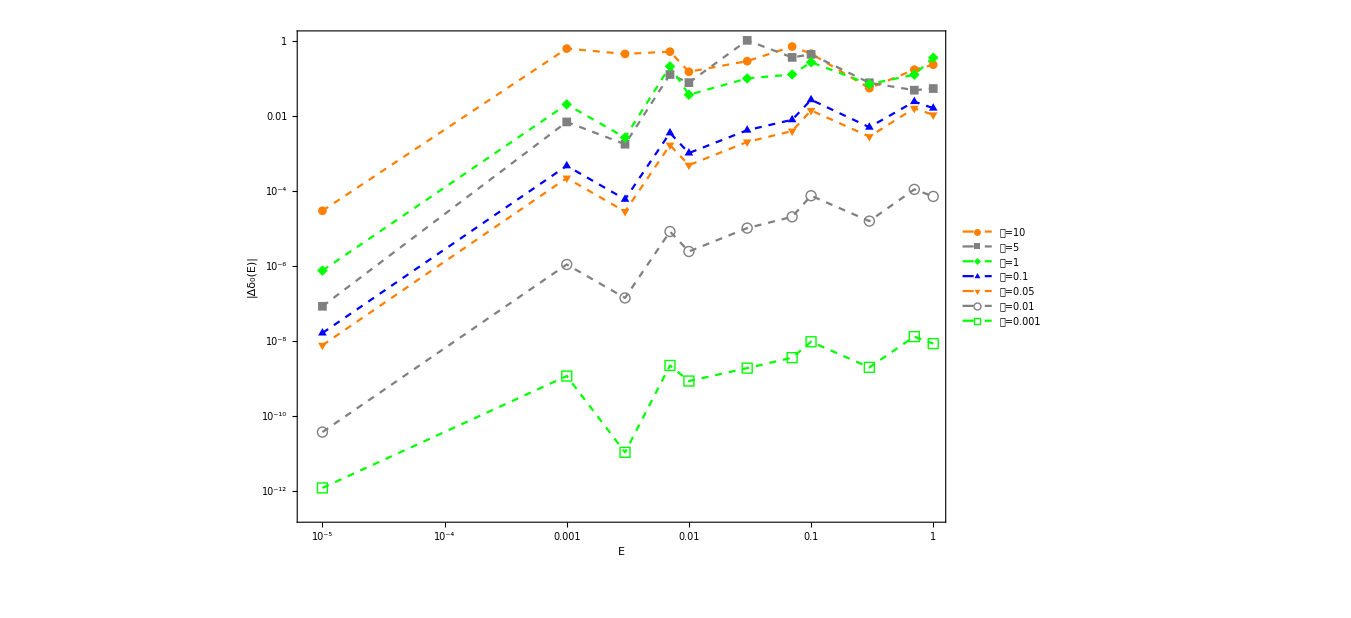

```mathematica
ListLogLogPlot[Table[Drop[La[[n]],1],{n,Length@aa}],Frame->True,Joined->True,PlotMarkers->Automatic,ImageSize->1000,FrameLabel->{"E","|Δδ_0(E)|"},RotateLabel->False,PlotStyle->{{Dashed,Orange},{Dashed,Gray},{Dashed,Green},{Dashed,Blue}},PlotLegends->(("𝒶="<>ToString[#])&/@aa)]
Export["C:\\Users\\ASUS\\OneDrive\\文档\\Test_6\\Test_Coulomb_Various_a_1.eps",%];
```

```mathematica
a=;
```

## Calculating eigenenergy of Coulomb Potential

```mathematica
EigenEnergy[V[r],αSch]
```

## Determine 𝒸_1 in V_eff^(a^2)

```mathematica
hhhc[en_,c1_?NumberQ]:=δ50e[en,Vs1[r,a,c1]];
evnhhhc[c1_]:=N[hhhc[10^-10,c1]-δ50e[10^-10,V[r]],8];
Determinec1:=Module[{aaa,findroot},aaa=a;
Print[a];findroot=FindRoot[hhhc1[10^-10,aaa,c1]==δ50e[10^-10,V[r]],{c1,-40},MaxIterations->10000,AccuracyGoal->30,PrecisionGoal->30,WorkingPrecision->80,StepMonitor:>Print[{c1,evnhhhc1[aaa,c1]}]];
Print[c1/.findroot];
c1/.findroot
]
```

```mathematica
c1=Determinec1
```

```mathematica
energyVs1=EigenEnergy[Vs1[r,a,c1],αSch]
```

```mathematica
δVs1=δ50[Vs1[r,a,c1]]
```

## Determine 𝒸_2 and 𝒹_1 in V_eff^(a^4)

```mathematica
hhh[en_,c2_?NumberQ,d1_?NumberQ]:=δ50e[en,Vs2[r,a,c2,d1]]
evnhhh1:=N[hhh[ee[[1]],c2,d1]-δ50e[ee[[1]],V[r]],8];
evnhhh2:=N[hhh[ee[[2]],c2,d1]-δ50e[ee[[2]],V[r]],8];
```

```mathematica
Determinec2d1:=Module[{findroot},
findroot=FindRoot[{hhh[ee[[1]],c2,d1]==δ50e[ee[[1]],V[r]],hhh[ee[[2]],c2,d1]==δ50e[ee[[2]],V[r]]},{{c2,-40.},{d1,3.}},MaxIterations->10000,AccuracyGoal->12,WorkingPrecision->50,StepMonitor:>Print[{c2,d1,evnhhh1,evnhhh2}]];
{c2,d1}/.findroot
]
```

```mathematica
{c2,d1}=Determinec2d1
```

```mathematica
energyVs2=EigenEnergy[Vs2[r,a,{c2,d1}],αSch]
```

```mathematica
δVs2=δ50[Vs2[r,a,{c2,d1}]]
```

## Matrix element <p^4>

```mathematica
nRange=20;
```

```mathematica
p4Ture[n_,b_][Z_,γ_,η_,opt___]:=Z NIntegrate[(Laplacian[efVs2[[n]],{r}]^2),{r,0,b},opt]+γ/a NIntegrate[efVs2[[n]]^2 δa[r],{r,0,b},opt]+η a NIntegrate[efVs2[[n]]^2 Laplacian[δa[r],{r,θ,ϕ},"Spherical"],{r,0,b},opt]
```

```mathematica
REAL=Table[Integrate[D[r RS[n,r],{r,2}]^2,{r,0,∞}],{n,nRange}];
REF=Table[Integrate[D[r RS[n,r],{r,2}]^2,{r,0,∞}],{n,nRange-2,nRange}];
```

### Matrix element in V_eff^(a^2)

```mathematica
efVs1=Module[{ef,am},
ef=Eigenfun[Vs1[r,a,c1],energyVs1];
am=NIntegrate[f[r]^2/.#,{r,1.*10^-50,2000}]^-0.5&/@ef;
(am[[2#]]=-am[[2#]])&@Range@10;
Table[am[[n]]f[r]/.ef[[n]],{n,20}]
]
```

```mathematica
AbsoluteTiming@GraphicsGrid@Partition[Table[Plot[{(RS[n,r]r),efVs1[r]},{r,0,2000},PlotRange->Full,ImageSize->Medium,PlotStyle->{Blue,Orange}],{n,20}],4]
AbsoluteTiming@GraphicsGrid@Partition[Table[Plot[(RS[n,r]r)-efVs1[r],{r,0,2000},PlotRange->Full,ImageSize->Medium],{n,20}],4]
```

```mathematica
FALSEVs1=NIntegrate[D[efVs1[[#]],{r,2}]^2,{r,0,2000},{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@Range@nRange
N[%,6]
Abs@((REAL-FALSEVs1)/REAL);
N[%,6]
```

```mathematica
RESVs1=FindRoot[Evaluate@Thread[(p4Ture[#,2000][Z,γ,η,{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@{10,15,20})==(REF[[#]]&/@{1,2,3})](*/.Z->1*),{{Z,1.1,1.12},{γ,0,100},{η,100,-2}},WorkingPrecision->50,AccuracyGoal->6,PrecisionGoal->6]
```

```mathematica
p4Vs1=p4Ture[#,2000][Z,γ,η,{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@Range@nRange/.RESVs1;
N[%,6]
Abs[(p4Vs1-REAL)/REAL];
N[%,6]
```

### Matrix element in V_eff^(a^4)

```mathematica
efVs2=Module[{ef,am},
ef=Eigenfun[Vs2[r,a,c1],energyVs2];
am=NIntegrate[f[r]^2/.#,{r,1.*10^-50,2000}]^-0.5&/@ef;
(am[[2#]]=-am[[2#]])&@Range@10;
Table[am[[n]]f[r]/.ef[[n]],{n,20}]
]
```

```mathematica
AbsoluteTiming@GraphicsGrid@Partition[Table[Plot[{(RS[n,r]r),efVs1[r]},{r,0,2000},PlotRange->Full,ImageSize->Medium,PlotStyle->{Blue,Orange}],{n,20}],4]
AbsoluteTiming@GraphicsGrid@Partition[Table[Plot[(RS[n,r]r)-efVs1[r],{r,0,2000},PlotRange->Full,ImageSize->Medium],{n,20}],4]
```

```mathematica
FALSEVs2=NIntegrate[D[efVs2[[#]],{r,2}]^2,{r,0,2000},{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@Range@nRange
N[%,6]
Abs@((REAL-FALSE)/REAL);
N[%,6]
```

```mathematica
RESVs2=FindRoot[Evaluate@Thread[(p4Ture[#,2000][Z,γ,η,{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@{10,15,20})==(REF[[#]]&/@{1,2,3})](*/.Z->1*),{{Z,1.1,1.12},{γ,0,100},{η,100,-2}},WorkingPrecision->50,AccuracyGoal->6,PrecisionGoal->6]
```

```mathematica
p4Vs2=p4Ture[#,2000][Z,γ,η,{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@Range@nRange/.RESVs2;
N[%,6]
Abs[(p4Vs2-REAL)/REAL];
N[%,6]
```